## INFO :

## Read in .dat files :

```mathematica
(*myFolder = "C:\\Users\\Charlotte\\Dropbox (Personal)\\_copy_old lab NB notes\\"
```

```mathematica
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes"
```

/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes

```mathematica
myNT2=<<(myFolder<>"/102017_Imaging_14-5h_results_NT.dat");
myTA2=<<(myFolder<>"/102017_Imaging_14-5h_results_TA.dat");
myTL2=<<(myFolder<>"/102017_Imaging_14-5h_results_TL.dat");
myTA1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_TA.dat");
myNT1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_NT.dat");
myTA3=<<(myFolder<>"/120317_Imaging_14-5h_results_TA.dat");
myNT3=<<(myFolder<>"/120317_Imaging_14-5h_results_NT.dat");
myTL3=<<(myFolder<>"/120317_Imaging_14-5h_results_TL.dat");
```

```mathematica
myNT -> 18, 13,25
myTA -> 13, 18, 26
myTL ->  , 13, 18
```

```mathematica
myTL2//Dimensions
myTL3//Dimensions
```

{13,7,1}

{18,2,1}

## Binning based on #RNA in cell at frame # (choose 2, 3, 4, 5, or 6)

```mathematica
NTdata = Join[myNT1, myNT2];
TAdata = Join[myTA1, myTA2];
TLdata = Join[myTL2];
```

```mathematica
(*
m = 20
n = 80
o = 3
NTdataL=Cases[NTdata,x_/;x[[2,1,o,2]]<m];
NTdataM=Cases[NTdata,x_/;m≤x[[2,1,o,2]]≤n];
NTdataH=Cases[NTdata,x_/;n<x[[2,1,o,2]]];
TAdataL=Cases[TAdata,x_/;x[[2,1,o,2]]<m];
TAdataM=Cases[TAdata,x_/;m≤x[[2,1,o,2]]≤n];
TAdataH=Cases[TAdata,x_/;n<x[[2,1,o,2]]];
TLdataL=Cases[TLdata,x_/;x[[2,1,o,2]]<m];
TLdataM=Cases[TLdata,x_/;m≤x[[2,1,o,2]]≤n];
TLdataH=Cases[TLdata,x_/;n<x[[2,1,o,2]]];
*)
```

```mathematica
rmNTdata = NTdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
m = 20;
n = 60;
o = 4;
p=2;
NTdata0= rmNTdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
```

```mathematica
(*
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata/.""->0.//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata/.""->0.//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
*)
```

```mathematica
NTdata[[5,2,1,2,2]]
```

44.

```mathematica
NTdata[[All,2,1,o,2]]
```

{16.,15.,64.,22.,44.,37.,26.,45.,50.,120.,11.,71.,41.,125.,86.,54.,24.,20.,13.,13.,18.,45.,,13.,55.,12.,,48.,20.,12.,19.}

```mathematica
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
```

TA  31   inc 4   lo 10   med 11   hi 2

NT  31   inc 3   lo 9   med 15   hi 2

TL  13   inc 4   lo 0    med 5    hi 3

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

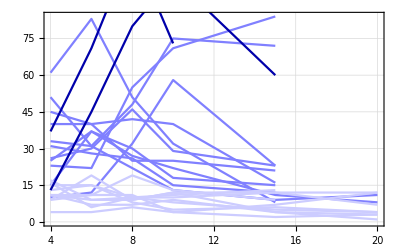

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

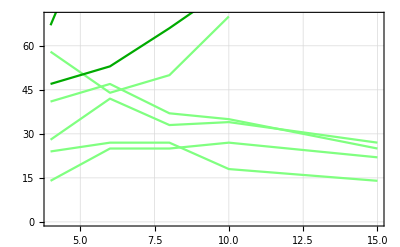

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

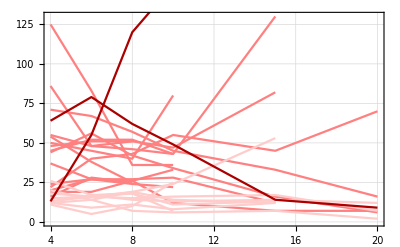

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

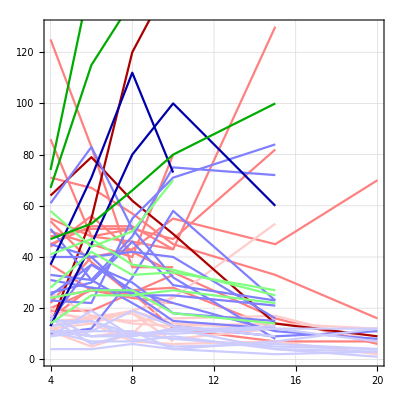

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

#### %Translation :

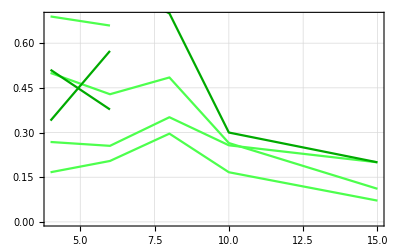

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

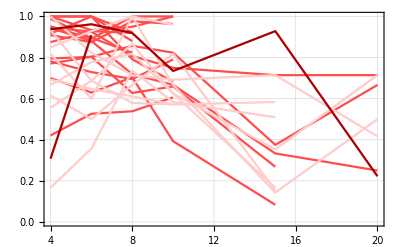

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

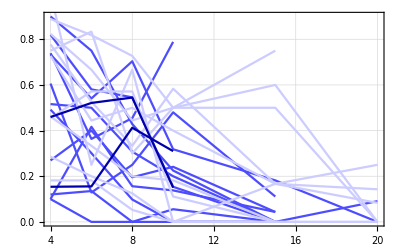

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

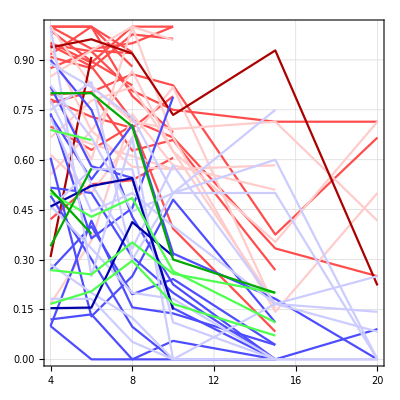

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

#### # Tethered :

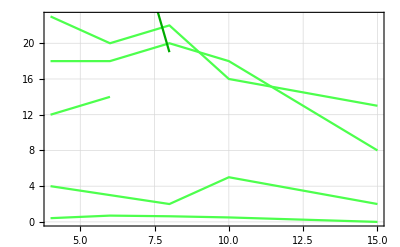

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

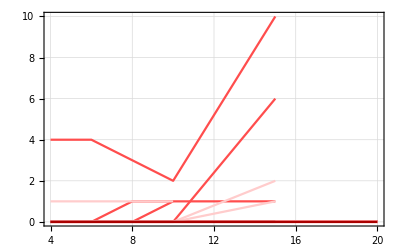

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

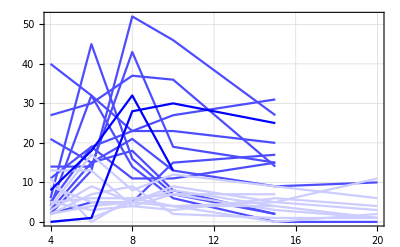

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

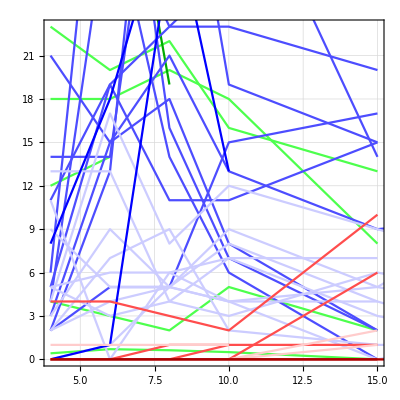

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

#### % cy3 accumulation :

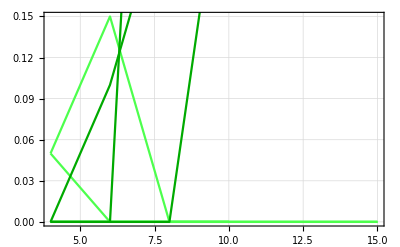

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

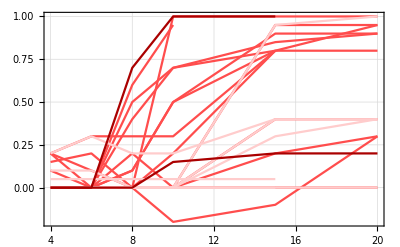

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

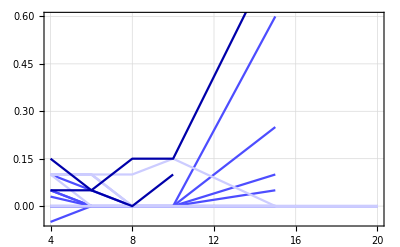

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

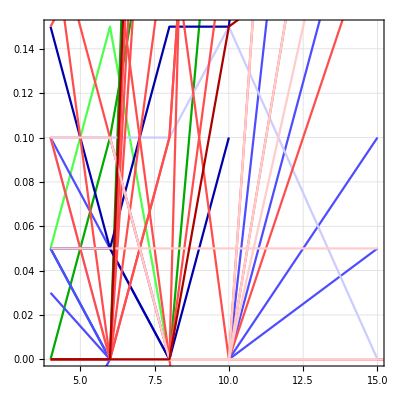

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

### Totals :

Binned by # RNA per cell at Frame 4 : <20,  20-80,  <80

TA  31   inc 0   lo 24   med 5   hi 1

NT  31   inc 0   lo 13   med 11   hi 9

TL  13   inc 0   lo 9    med 1    hi 2

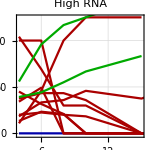
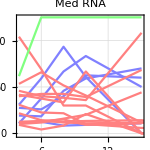
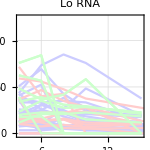

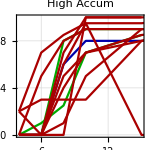
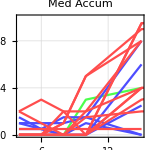
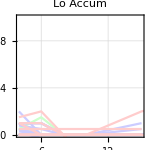

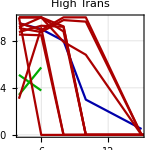
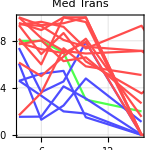

```mathematica
Row[{StringForm["Binned by # RNA per cell at Frame `` : <20,  20-80,  <80   ",o]}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[prnaTAH,prnaNTH,prnaTLH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTAM,prnaNTM,prnaTLM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,prnaTLL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150]
}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]

(*
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore!   "}]
*)
```

## Binning based on Accumulation in cell at frames 1-5

```mathematica
NTdata//Dimensions
TAdata//Dimensions
TLdata//Dimensions
```

{31,7,1}

{31,7,1}

{13,7,1}

```mathematica
NTdata =Join[myNT1,myNT2];
TAdata = Join[myTA1,myTA2];
TLdata = Join[myTL2];
```

```mathematica
(* 
TLdata = myTL2⟦4,Flatten@Position[myTL2⟦4⟧,""]⟧=0
```

```mathematica
rmNTdata = NTdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
(* USE THESE INSTEAD if you dont want to remove high accum data... 


NTdata0= NTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= NTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= NTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
NTdataH= NTdata/.""->0.//Cases[#,x_/; 1.≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= TAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TAdataL= TAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= TAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1.]&;
TAdataH= TAdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= TLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TLdataL= TLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= TLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
TLdataH= TLdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
```

```mathematica
p = 1.5
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; p≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TAdataL= rmTAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1p]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TLdataL= rmTLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
```

1.5

```mathematica
Table[Total[TLdata[[j,4,1,2;;6,2]]],{j,1,Length@TLdata,1}]
```

{0.+3 ,0.+3 ,1.9,2.6,0.,0.+3 ,0.+,0.2,0.+,4 +f,0.05,0.7,0.05+4 }

```mathematica
(*
NTdata0=NTdata//Cases[#,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataM=Cases[NTdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
NTdataH=Cases[NTdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TAdata0=Cases[TAdata,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus];TAdataL=Cases[TAdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
TAdataM=Cases[TAdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]<.75];
TAdataH=Cases[TAdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TLdata0=TLdata//Cases[3,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;TLdataL=Cases[TLdata,x_/; 0≤Total[x[[4,1,2;;6,2]]]<.25];
TLdataM=Cases[TLdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
TLdataH=Cases[TLdata,x_/; .75≤Total[x[[4,1,2;;6,2]]]];
```

```mathematica
Row[{"TA  ",Length@TAdata ," " ,Length@TAdata0," " ,Length@TAdataL ," " ,Length@TAdataM ," " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ," " ,Length@NTdata0," " ,Length@NTdataL ," " ,Length@NTdataM ," " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ," " ,Length@TLdata0," " ,Length@TLdataL ," " ,Length@TLdataM ," " ,Length@TLdataH}]
```

TA  31 0 24 4 2

NT  31 0 13 5 14

TL  13 0 9 1 2

TA  31 0 24 4 2

NT  31 0 13 7 13

TL  13 0 9 1 2

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

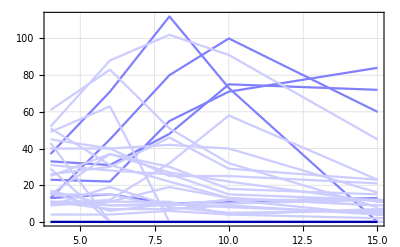

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

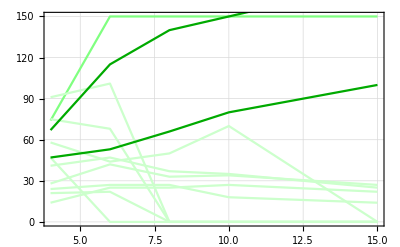

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

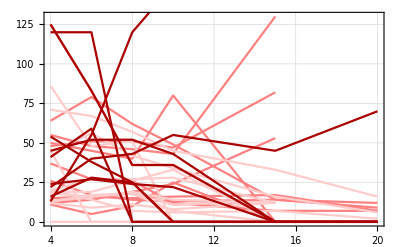

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

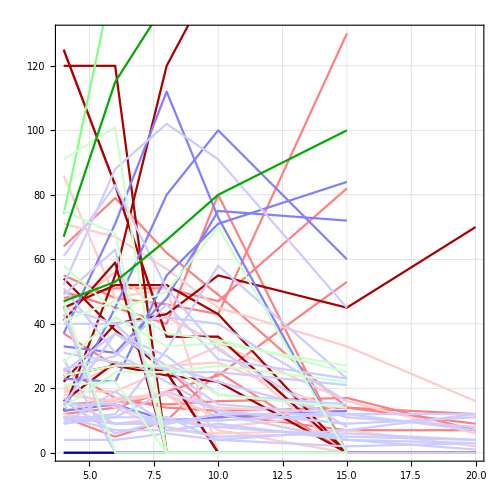

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

#### %Translation :

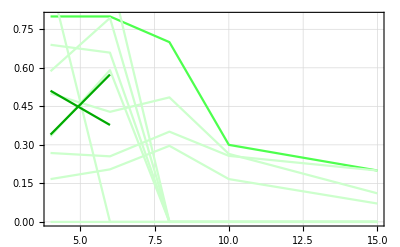

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

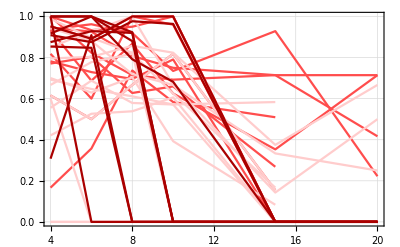

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

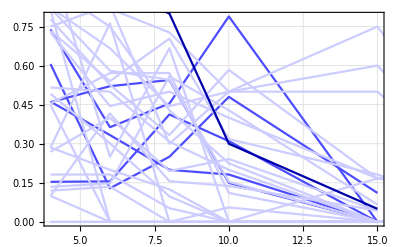

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

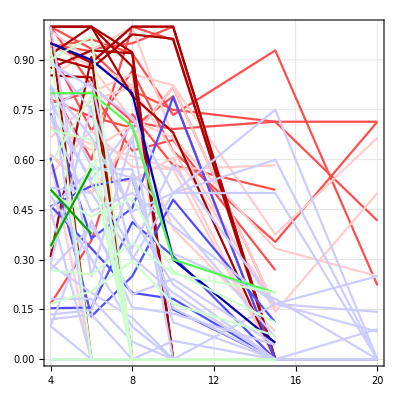

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

#### # Tethered :

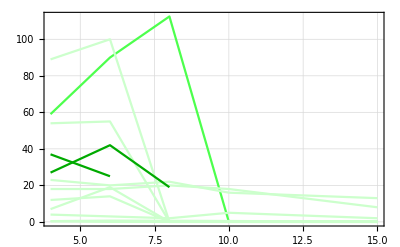

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

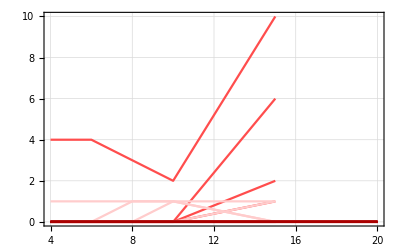

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

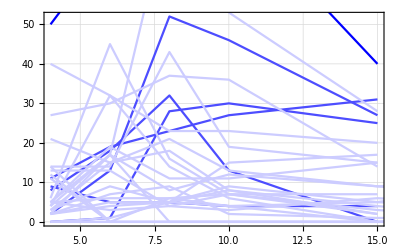

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

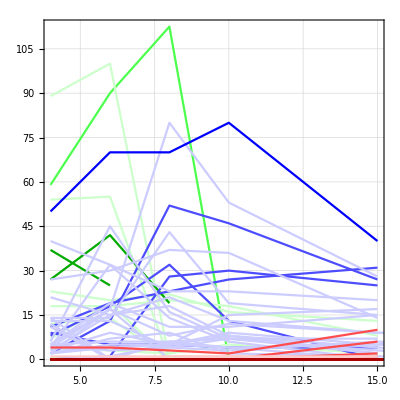

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

#### % cy3 accumulation :

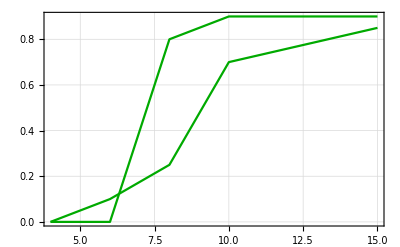

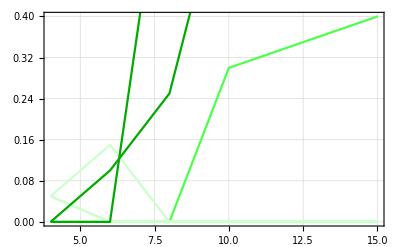

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

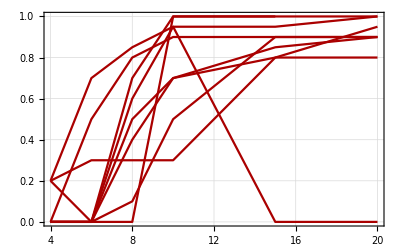

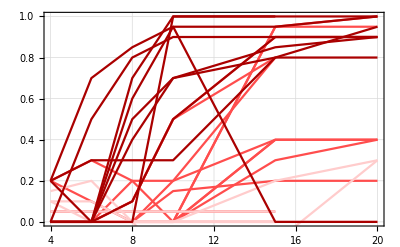

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

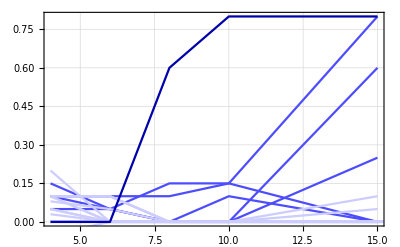

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

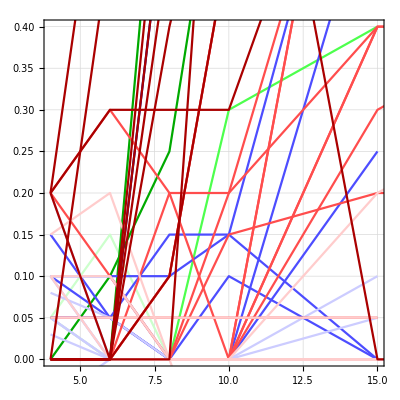

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

#### Totals :

Binned by % accumulation: <25%,  25-75%,  >75%

TA  31   inc 0   lo 24   med 5   hi 1

NT  31   inc 0   lo 13   med 11   hi 9

TL  13   inc 0   lo 9    med 1    hi 2

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

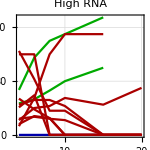
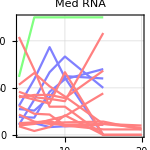
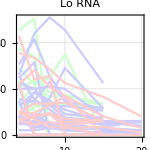

***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!

```mathematica
Row[{"Binned by % accumulation: <25%,  25-75%,  >75%"}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[prnaTLH,prnaTAH,prnaNTH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLM,prnaTAM,prnaNTM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{0,All}},ImageSize->150]
}]
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!"}]
```

NOTE!!! This is neglecting that since I’m doing the total I’m not actually 
doing 50-75% or over 75% or whatever, I’m totalling multiple points!!!

### Calculating the averages of replicate data set means....

```mathematica
Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
Table[{AvgtethNT2[[i]],AvgtethNT1[[i]]},{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
Mean/@Table[AvgtethNT2[i],{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
totalAvgtethNT=Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
totalAvgtethNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

{}

-Graphics-